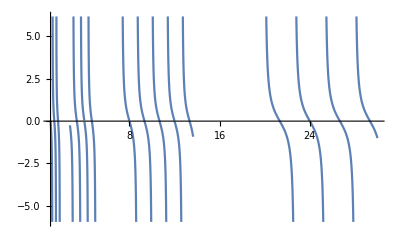

0.32492

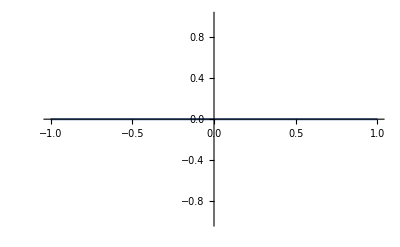

```mathematica
ClearAll["Global`*"];
r[t_]:=(x=-Sin[t];y=Cos[t];{x,y});
line[x_,t_,f_,g_]:=If[r[2Pi*g[f[t]]][[1]]-r[2Pi*g[t]][[1]]!=0,(x-r[2Pi*g[t]][[1]])*(r[2Pi*g[f[t]]][[2]]-r[2Pi*g[t]][[2]])/(r[2Pi*g[f[t]]][[1]]-r[2Pi*g[t]][[1]]),0];


deriv[t_,f_,g_]:=-(r[2Pi*g[f[t]]][[2]]-r[2Pi*g[t]][[2]])/(r[2Pi*g[f[t]]][[1]]-r[2Pi*g[t]][[1]]);
generateDerivPlot[f_,g_]:= (
start=1;
stop=30;
Plot[deriv[t,f,g],{t,start,stop}]
);
f[n_]:=n*4;
g[n_]:=n/2^Floor[Log[n]];
integ[t_,f_,g_]:=Integrate[deriv[t,f,g],t];
generateDerivPlot[f,g]
Print[(r[2Pi*g[f[3.4]]][[2]]-r[2Pi*g[3.4]][[2]])/(r[2Pi*g[f[3.4]]][[1]]-r[2Pi*g[3.4]][[1]])];
Plot[line[x,1.1,f,g],{x,-1,1}]

(*
ParametricPlot[{r[2Pi*g[t]][[1]]+t*(r[2Pi*g[f[t]]][[1]]-r[2Pi*g[t]][[1]]),r[2Pi*g[t]][[2]]+t*(r[2Pi*g[f[t]]][[2]]-r[2Pi*g[t]][[2]])},{t,0,1000}]
*)
(*
Print[deriv[t,f,g]];
Print[integ[t,f,g]];
Integrate[(Cos[2^(1-Floor[Log[t]]) π t]-Cos[2^(3-Floor[Log[4 t]]) π t])/(Sin[2^(1-Floor[Log[t]]) π t]-Sin[2^(3-Floor[Log[4 t]]) π t]),t]
*)
```